```mathematica
Quit
```

## Load FeynCalc

```mathematica
(*$LoadFeynArts=True;*)
$LoadAddOns={"FeynHelpers","FeynArts"};
<<FeynCalc`;
$FAVerbose=False;
FAPatch[PatchModelsOnly->True]
```

FeynCalc 9.3.0 (stable version). For help, use the documentation center, check out the wiki or write to the mailing list.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, P3H-20-002, TTP19-020, TUM-EFT 130/19, arXiv:2001.04407

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

FeynHelpers 1.2.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

FeynArts 3.11 (2 Sep 2019) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

Patched 2 FeynArts models.

```mathematica
model="HiggsPortalDM";
genericModel={"Lorentz",model};
```

## Tools

### Utilities

```mathematica
ComputeMandelstamTBound[M_,m1_,m2_,m3_,s_,t_]:=Module[{E1,E2},E1=(M^2+m1^2-s)/(2*M);
E2=(M^2+m2^2-t)/(2*M);
Solve[M^2+2*E1*E2+m1^2+m2^2-m3^2-2*M*(E1+E2)==2Sqrt[(E1^2-m1^2)*(E2^2-m2^2)],t]];
```

```mathematica
KallenLambda[a_,b_,c_]:=a^2+b^2+c^2-2*(a*b+a*c+b*c);
```

```mathematica
CorrectParameters[expr_]:=expr/.{
SMP["m_H"]->MH,
SMP["m_W"]->MW,
SMP["m_Z"]->MZ,
SMP["m_t"]->MTOP,
SMP["m_b"]->MB,
SMP["e"]->√(4π alphaEM),

FCGV["MH"]->MH,
FCGV["MZ"]->MZ,
FCGV["MW"]->MW,
FCGV["MT"]->MTOP,
FCGV["MB"]->MB,

FCGV["EL"]->√(4π alphaEM),
Plus[cw^2,sw^2]:>1,
SUNFDelta[SUNFIndex[a_],SUNFIndex[b_]]^2:>Ncol
}
```

```mathematica
x^-2/.{Power[x_,pow:2|3|4|5|6]:>ToExpression["pow"<>ToString[pow]<>"["<>ToString[x]<>"]"],
Power[x_,pow:-2|-3|-4|-5|-6]:>1/ToExpression["pow"<>ToString[Abs[pow]]<>"["<>ToString[x]<>"]"]}
```

1/(pow2(x))

```mathematica
ToCForm[expr_]:=expr//.{e->√(4π alphaEM),Csc[x_]:>1/Sin[x],Sec[x_]:>1/Cos[x],Pair[Momentum[a_],Momentum[b_]]:>MDOT[a,b],Power[x_,pow:2|3|4|5|6]:>ToExpression["pow"<>ToString[pow]<>"["<>ToString[x]<>"]"],
Power[x_,pow:-2|-3|-4|-5|-6]:>1/ToExpression["pow"<>ToString[Abs[pow]]<>"["<>ToString[x]<>"]"]}//ToString[#,CForm]&//StringReplace[#,{"Power"->"pow","Tan"->"tan","Cos"->"cos","MNe"->"Mn","MNue"->"Mnu","mixe"->"theta","vev"->"VevH","Sin"->"sin","Pi"->"M_PI","Me"->"Ml","ΓH"->"WidthH","ΓZ"->"WidthZ","ΓW"->"WidthW","Sqrt"->"sqrt","Complex(0,1)"->"im","MTOP"->"Mq","ΓNe"->"WidthN","ye"->"yukl","Log"->"log"}]&
```

### Particles

```mathematica
(*determine if state is a fermion*)isFermion[state_]:=Module[{head},(*if state looks like-F[1],need to strip off the `Times` head*)head=If[Head[state]===Times,Head[ReplaceAll[state,Times[a_,b__]:>b]],Head[state]];
head===FeynArts`F||head===FeynArts`U];

(*determine if state is a vector*)
isVector[state_]:=Module[{head},(*if state looks like-V[1],need to strip off the `Times` head*)head=If[Head[state]===Times,Head[ReplaceAll[state,Times[a_,b__]:>b]],Head[state]];
head===FeynArts`V];
```

```mathematica
ElectronNeutrino=F[1,{1}];
MuonNeutrino=F[1,{2}];
TauNeutrino=F[1,{3}];
Electron=F[2,{1}];
Muon=F[2,{2}];
Tau=F[2,{3}];
UpQuark=F[3,{1}];
CharmQuark=F[3,{2}];
TopQuark=F[3,{3}];
DownQuark=F[4,{1}];
StrangeQuark=F[4,{2}];
BottomQuark=F[4,{3}];
DM=F[5];
Higgs=S[1];
ScalarMediator=S[4];
Photon=V[1];
ZBoson=V[2];
WBoson=V[3];
```

### Diagrams

```mathematica
Options[GenerateDiagrams]={FeynArts`LoopNumber->0,FeynArts`Adjacencies->{3,4,5},FeynArts`ExcludeParticles->{},FeynArts`ExcludeTopologies->{FeynArts`Tadpoles,FeynArts`SelfEnergies,FeynArts`WFCorrections},FeynArts`InsertionLevel->{FeynArts`Particles},FeynArts`Paint->False,FeynArts`ColumnsXRows->OptionValue[FeynArts`Paint,FeynArts`ColumnsXRows]};

GenerateDiagrams[inStates_,outStates_,OptionsPattern[]]:=Block[{tops,diags},tops=FeynArts`CreateTopologies[OptionValue[FeynArts`LoopNumber],Length[inStates]->Length[outStates],FeynArts`ExcludeTopologies->OptionValue[FeynArts`ExcludeTopologies],FeynArts`Adjacencies->OptionValue[FeynArts`Adjacencies]];
diags=FeynArts`InsertFields[tops,inStates->outStates,FeynArts`InsertionLevel->OptionValue[FeynArts`InsertionLevel],Model->{model},GenericModel->genericModel,FeynArts`ExcludeParticles->OptionValue[FeynArts`ExcludeParticles]];
If[OptionValue[FeynArts`Paint],FeynArts`Paint[diags,FeynArts`ColumnsXRows->OptionValue[FeynArts`ColumnsXRows]],FeynArts`SheetHeader->None];
diags];
```

### Unstable Propagator

```mathematica
GetWidth[SMP["m_H"]|MH]=ΓH;
GetWidth[SMP["m_Z"]|MZ]=ΓZ;
GetWidth[SMP["m_W"]|MW]=ΓW;
GetWidth[MSM]=ΓSM;

SubstituteUnstablePropagator[expr_]:=expr/.{
FeynAmpDenominator[PropagatorDenominator[Momentum[a__],m:SMP["m_H"]|MH|SMP["m_Z"]|MZ|SMP["m_W"]|MW|MSM]]:>Den[ScalarProductExpand[SP[a,a]]-m^2+I*GetWidth[m]*m]
}
Den/:Times[Den[a__],Den[b__]]:=Den[a*b]
```

### Amplitudes

```mathematica
Options[ComputeAmplitude]:={FeynArts`LoopNumber->0,FeynArts`Adjacencies->{3,4,5},FeynArts`ExcludeParticles->{},FeynArts`ExcludeTopologies->{FeynArts`Tadpoles,FeynArts`SelfEnergies,FeynArts`WFCorrections},
FeynArts`InsertionLevel->{FeynArts`Particles},
FeynArts`Paint->False,
FeynArts`ColumnsXRows->OptionValue[FeynArts`Paint,FeynArts`ColumnsXRows],
FeynCalc`ChangeDimension->4,FeynCalc`FinalSubstitutions->{},
FeynCalc`IncomingMomenta->OptionValue[FeynCalc`FCFAConvert,FeynCalc`IncomingMomenta],
System`List->False,
FeynCalc`LoopMomenta->OptionValue[FeynCalc`FCFAConvert,FeynCalc`LoopMomenta],
FeynCalc`LorentzIndexNames->{Global`μ,Global`ν,Global`α,Global`β,Global`ρ,Global`σ},
FeynCalc`OutgoingMomenta->OptionValue[FeynCalc`FCFAConvert,FeynCalc`OutgoingMomenta],
FeynCalc`SMP->True,
FeynCalc`TransversePolarizationVectors->OptionValue[FeynCalc`FCFAConvert,FeynCalc`TransversePolarizationVectors],
FeynArts`GaugeRules->OptionValue[FeynArts`CreateFeynAmp,FeynArts`GaugeRules],
FeynArts`PreFactor->OptionValue[FeynArts`CreateFeynAmp,FeynArts`PreFactor],
FeynArts`Truncated->OptionValue[FeynArts`CreateFeynAmp,FeynArts`Truncated]};

ComputeAmplitude[inStates_,outStates_,OptionsPattern[]]:=Module[{ampFA,ampFC,diagrams},FeynCalc`ClearScalarProducts[];
(*create the topologies based on input states*)diagrams=GenerateDiagrams[inStates,outStates,FeynArts`LoopNumber->OptionValue[FeynArts`LoopNumber],FeynArts`Adjacencies->OptionValue[FeynArts`Adjacencies],FeynArts`ExcludeParticles->OptionValue[FeynArts`ExcludeParticles],FeynArts`ExcludeTopologies->OptionValue[FeynArts`ExcludeTopologies],FeynArts`InsertionLevel->OptionValue[FeynArts`InsertionLevel],FeynArts`Paint->OptionValue[FeynArts`Paint],FeynArts`ColumnsXRows->OptionValue[FeynArts`ColumnsXRows]];
(*Compute the amplitude*)ampFA=FeynArts`CreateFeynAmp[diagrams,FeynArts`GaugeRules->OptionValue[FeynArts`GaugeRules],FeynArts`PreFactor->OptionValue[FeynArts`PreFactor],FeynArts`Truncated->OptionValue[FeynArts`Truncated]];
ampFC=FeynCalc`FCFAConvert[ampFA,FeynCalc`IncomingMomenta->OptionValue[FeynCalc`IncomingMomenta],FeynCalc`OutgoingMomenta->OptionValue[FeynCalc`OutgoingMomenta],FeynCalc`LorentzIndexNames->OptionValue[FeynCalc`LorentzIndexNames],FeynCalc`LoopMomenta->OptionValue[FeynCalc`LoopMomenta],FeynCalc`UndoChiralSplittings->True,FeynCalc`SMP->OptionValue[FeynCalc`SMP],FeynCalc`ChangeDimension->OptionValue[FeynCalc`ChangeDimension],FeynCalc`FinalSubstitutions->Join[OptionValue[FeynCalc`FinalSubstitutions],M$FACouplings],FeynCalc`TransversePolarizationVectors->OptionValue[FeynCalc`TransversePolarizationVectors],
FeynCalc`DropSumOver->True];
listPreProc=ampFC;
ampFC=Flatten[ampFC];
listPreProc1=ampFC;
ampFC=If[OptionValue[List],ampFC,Total[ampFC]];
listPreProc2=ampFC;
ampFC=ReplaceAll[ampFC,{FeynArts`FALeviCivita->FeynCalc`Eps,Global`FAFourVector->FeynCalc`Momentum}];
(*subsitute unstable propagator*)ampFC=Map[SubstituteUnstablePropagator,ampFC];
(*--THIS NEXT LINE IS OFFENDING--*)
(*ampFC=Map[FeynCalc`PropagatorDenominatorExplicit,ampFC];*)
ampFC=Map[FeynCalc`Contract,ampFC];
ampFC=Map[FeynCalc`DiracSimplify[#,FeynCalc`DiracSubstitute67->True]&,ampFC];
ampFC=Map[FeynCalc`ExpandScalarProduct,ampFC];
CorrectParameters[Map[Simplify,ampFC]]
];
```

### Amplitude Squared

```mathematica
Options[ComputeAmplitudeSquared]:={FeynArts`Adjacencies->{3,4,5},FeynArts`ExcludeParticles->{},FeynArts`ExcludeTopologies->{FeynArts`Tadpoles,FeynArts`SelfEnergies,FeynArts`WFCorrections},FeynArts`InsertionLevel->{FeynArts`Particles},FeynArts`Paint->False,FeynArts`ColumnsXRows->OptionValue[FeynArts`Paint,FeynArts`ColumnsXRows],FeynArts`GaugeRules->_FeynArts`FAGaugeXi->1,FeynArts`PreFactor->-I (2 π)^(-4 FeynArts`LoopNumber),FeynCalc`ChangeDimension->4,FeynCalc`FinalSubstitutions->{},FeynCalc`IncomingMomenta->{},FeynCalc`OutgoingMomenta->{},FeynCalc`SMP->True};


ComputeAmplitudeSquared[inStates_List,outStates_List,OptionsPattern[]]:=Module[{msqrd,amp,inMomenta,outMomenta,i},(*Create the amplitude*)amp=ComputeAmplitude[inStates,outStates,FeynArts`Adjacencies->OptionValue[FeynArts`Adjacencies],FeynArts`ExcludeParticles->OptionValue[FeynArts`ExcludeParticles],FeynArts`ExcludeTopologies->OptionValue[FeynArts`ExcludeTopologies],FeynArts`InsertionLevel->OptionValue[FeynArts`InsertionLevel],FeynArts`Paint->OptionValue[FeynArts`Paint],FeynArts`ColumnsXRows->OptionValue[FeynArts`ColumnsXRows],FeynArts`GaugeRules->OptionValue[FeynArts`GaugeRules],FeynArts`PreFactor->OptionValue[FeynArts`PreFactor],FeynCalc`ChangeDimension->OptionValue[FeynCalc`ChangeDimension],FeynCalc`FinalSubstitutions->OptionValue[FeynCalc`FinalSubstitutions],FeynCalc`IncomingMomenta->OptionValue[FeynCalc`IncomingMomenta],FeynCalc`OutgoingMomenta->OptionValue[FeynCalc`OutgoingMomenta],FeynCalc`SMP->OptionValue[FeynCalc`SMP]];
FeynCalc`ClearScalarProducts[];
(*determine incoming/outgoing momenta*)inMomenta=OptionValue[FeynCalc`IncomingMomenta];
outMomenta=OptionValue[FeynCalc`OutgoingMomenta];
(*Fix momenta-If user didn't specify momenta,populate them based on what FeynCalc does.*)For[i=Length[inMomenta]+1,i≤Length[inStates],i++,AppendTo[inMomenta,ToExpression["InMom"<>ToString[i]]]];
For[i=Length[outMomenta]+1,i≤Length[outStates],i++,AppendTo[outMomenta,ToExpression["OutMom"<>ToString[i]]]];
(*set masses*)
For[i=1,i≤Length[inMomenta],i++,FeynCalc`SP[inMomenta[[i]]]=FeynArts`TheMass[inStates[[i]]]^2;];
For[i=1,i≤Length[outMomenta],i++,FeynCalc`SP[outMomenta[[i]]]=FeynArts`TheMass[outStates[[i]]]^2];
(*Square it*)
msqrd=amp*FeynCalc`FCRenameDummyIndices[FeynCalc`ComplexConjugate[amp]];
(*If any of the in states are fermionic,average over spins*)For[i=1,i≤Length[inStates],i++,If[isFermion[inStates[[i]]],msqrd=FeynCalc`FermionSpinSum[msqrd,FeynCalc`ExtraFactor->1/2],Continue];];
(*If any of the out states are fermionic,sum over spins*)For[i=1,i≤Length[outStates],i++,If[isFermion[outStates[[i]]],msqrd=FeynCalc`FermionSpinSum[msqrd],Continue];];
(*actually perform the fermion spin sums*)
msqrd=ReplaceAll[msqrd,FeynCalc`DiracTrace->FeynCalc`TR];
(*If any of the states are vectors,do a sum over polarizations.*)(*Add 1/2 (1/3) massless (massive) initial state vectors*)For[i=1,i≤Length[inStates],i++,If[isVector[inStates[[i]]],If[FeynArts`TheMass[inStates[[i]]]===0,msqrd=(1/2)*FeynCalc`DoPolarizationSums[msqrd,inMomenta[[i]],0],msqrd=(1/3)*FeynCalc`DoPolarizationSums[msqrd,inMomenta[[i]]];],Continue];];
For[i=1,i≤Length[outStates],i++,If[isVector[outStates[[i]]],If[FeynArts`TheMass[outStates[[i]]]===0,msqrd=FeynCalc`DoPolarizationSums[msqrd,outMomenta[[i]],0],msqrd=FeynCalc`DoPolarizationSums[msqrd,outMomenta[[i]]];],Continue];];
msqrd=FeynCalc`Contract[msqrd];
msqrd=Collect[msqrd,Den[_],Simplify];
FeynCalc`ClearScalarProducts[];
CorrectParameters[msqrd]];
```

### Compute Width

```mathematica
Options[ComputeWidth]={FeynArts`Adjacencies->{3,4,5},FeynArts`ExcludeParticles->{},FeynArts`InsertionLevel->{FeynArts`Particles},FeynArts`Paint->False,FeynArts`ColumnsXRows->OptionValue[FeynArts`Paint,FeynArts`ColumnsXRows],FeynArts`GaugeRules->_FeynArts`FAGaugeXi->1,FeynCalc`ChangeDimension->4,FeynCalc`FinalSubstitutions->{},FeynCalc`SMP->True};

ComputeWidth[inState_,outStates_List,OptionsPattern[]]:=Module[{msqrd,P,p1,p2,M,m1,m2,pf,preFactor,E1,E2},
FeynCalc`ClearScalarProducts[];
(*Create the amplitude*)
msqrd=ComputeAmplitudeSquared[{inState},outStates,FeynArts`Adjacencies->OptionValue[FeynArts`Adjacencies],FeynArts`ExcludeParticles->OptionValue[FeynArts`ExcludeParticles],FeynArts`InsertionLevel->OptionValue[FeynArts`InsertionLevel],FeynArts`Paint->OptionValue[FeynArts`Paint],FeynArts`ColumnsXRows->OptionValue[FeynArts`ColumnsXRows],FeynArts`GaugeRules->OptionValue[FeynArts`GaugeRules],FeynCalc`ChangeDimension->OptionValue[FeynCalc`ChangeDimension],FeynCalc`FinalSubstitutions->OptionValue[FeynCalc`FinalSubstitutions],FeynCalc`IncomingMomenta->{P},FeynCalc`OutgoingMomenta->{p1,p2},FeynCalc`SMP->OptionValue[FeynCalc`SMP]];
M=FeynArts`TheMass[inState];
m1=FeynArts`TheMass[outStates[[1]]];
m2=FeynArts`TheMass[outStates[[2]]];
E1=(M^2+m1^2-m2^2)/(2*M);
E2=(M^2-m1^2+m2^2)/(2*M);
FeynCalc`SP[P,P]=M^2;
FeynCalc`SP[p1,p1]=m1^2;
FeynCalc`SP[p2,p2]=m2^2;
FeynCalc`SP[P,p1]=M*E1;
FeynCalc`SP[P,p2]=M*E2;
FeynCalc`SP[p1,p2]=(M^2-m1^2-m2^2)/2;
msqrd=Simplify[msqrd];
pf=Sqrt[E1^2-m1^2];(*mag.of final state 3-momentum*)
preFactor=Simplify[(4*π)/(2*M)*pf/(16*Pi^2*M)];
(*If final state particles are identical,divide by 2*)
preFactor*=If[outStates[[1]]===outStates[[2]],1/2,1];
CorrectParameters[preFactor*msqrd]
]/;And[SameQ[Length[outStates]==2],SameQ[Length[inState]==0]];
```

## χχ->f+f

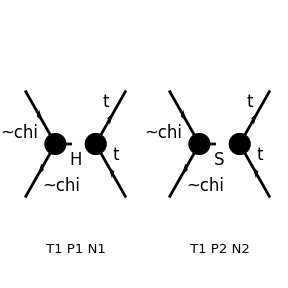

1/(2 vev)gSXX MTOP smix √(2-2 smix^2) δ_Col3Col4 (φ(-OverBar[p2],MDM)).(φ(OverBar[p1],MDM)) (φ(OverBar[p3],MTOP)).(φ(-OverBar[p4],MTOP)) (Den(2 (OverBar[p3]·OverBar[p4])+OverBar[p3]^2+OverBar[p4]^2-MH^2+ⅈ ΓH MH)-Den(2 (OverBar[p3]·OverBar[p4])+OverBar[p3]^2+OverBar[p4]^2-MSM^2+ⅈ ΓSM MSM))

```mathematica
ComputeAmplitude[{DM,-DM},{TopQuark,-TopQuark},Paint->True,IncomingMomenta->{p1,p2},OutgoingMomenta->{p3,p4},ColumnsXRows->{2,1}]/.{Conjugate[yu[3,3]]->MTOP/vev,yu[3,3]->MTOP/vev}//Simplify
```

## h+h->(W+) +( W-)

```mathematica
TopHHWW=CreateTopologies[0,2->2];
DiagamsHHWW=InsertFields[TopHHWW,{S[1],S[1]}->{V[3],-V[3]},InsertionLevel->{Particles},
                       Model->model,GenericModel->genericModel];
Paint[DiagamsHHWW,ColumnsXRows->{3,2}];
```

```mathematica
Options[CreateFeynAmp]
```

```mathematica
AmplitudesHHWW=CreateFeynAmp[DiagamsHHWW]/.M$FACouplings;
```

```mathematica
(* Look at the momenta *)
AmplitudesHHWW/.FeynAmpList[Rule[Process,x_],__][__]:>x
```

```mathematica
(* Extract only the amplitudes *)
AmplitudesHHWW/.{FeynAmpList[__][x__]:>List[x]}/.{FeynAmp[__,x_]:>x}//Simplify
```

## Z0+Z0->(W+) +( W-)

```mathematica
TopZZWW=CreateTopologies[0,2->2];
DiagamsZZWW=InsertFields[TopZZWW,{V[2],V[2]}->{V[3],-V[3]},InsertionLevel->{Particles},
                       Model->model,GenericModel->genericModel];
Paint[DiagamsZZWW,ColumnsXRows->{3,2}];
```

```mathematica
AmplitudesZZWW=CreateFeynAmp[DiagamsZZWW]/.M$FACouplings;
```

```mathematica
(* Look at the momenta *)
AmplitudesZZWW/.FeynAmpList[Rule[Process,x_],__][__]:>x
```

```mathematica
(* Extract only the amplitudes *)
AmplitudesZZWW/.{FeynAmpList[__][x__]:>List[x]}/.{FeynAmp[__,x_]:>x}//Simplify
```

## h->h at 1-Loop

```mathematica
Top2H1L=CreateTopologies[1,1->1, ExcludeTopologies->{Reducible}];
Diagams2H1L=InsertFields[Top2H1L,{S[1]}->{S[1]},InsertionLevel->{Particles},
                       Model->model,GenericModel->genericModel];
Paint[Diagams2H1L,ColumnsXRows->{4,2},ImageSize->{400,200},SheetHeader->None];
```

```mathematica
Amplitudes2H1L=CreateFeynAmp[Diagams2H1L]/.M$FACouplings;
```

```mathematica
(* Look at the momenta *)
Amplitudes2H1L/.FeynAmpList[Rule[Process,x_],__][__]:>x
```

```mathematica
(* Extract only the amplitudes *)
Amplitudes2H1L/.{FeynAmpList[__][x__]:>List[x]}/.{FeynAmp[__,x_]:>x}
```